In this part, we will calculate the eigenvalues along different paths in the 2D phase diagram, which reveals the meaning of different phases.

## Projection of Phase Diagram

```mathematica
Clear["Global`*"]
```

```mathematica
ham[Δ_,Ω_,γ_]:=Evaluate[{{Δ-I γ,1,Ω/2},{1,Δ+I γ,Ω/2},{Ω/2,Ω/2,0}}];
ham[Δ,Ω,γ]//MatrixForm
disc[Δ_,Ω_,γ_]:=Evaluate[Discriminant[Det[ham[Δ,Ω,γ]-IdentityMatrix[3]e],e]]
Simplify[Expand[Simplify[disc[Δ,Ω,γ]]]-Expand[Simplify[disc[-Δ,Ω,γ]]]]
Collect[Det[IdentityMatrix[3]e-ham[Δ,Ω,γ]],e]
```

(-ⅈ γ+Δ | 1 | Ω/2
1 | ⅈ γ+Δ | Ω/2
Ω/2 | Ω/2 | 0)

{{-ⅈ γ+Δ,1,Ω/2},{1,ⅈ γ+Δ,Ω/2},{Ω/2,Ω/2,0}}

```mathematica
EP2Surf[Δ_,Ω_,γ_]:=Simplify[Discriminant[Det[ham[Δ,Ω,γ]-IdentityMatrix[3]e],e]]
EP2Surf[Δ,Ω,γ]
```

-4 γ^6+1/4 (-4+4 Δ+Ω^2)^2 (1+2 Δ+Δ^2+2 Ω^2)+γ^4 (-8 Δ^2+6 (2+Ω^2))-γ^2 (4 Δ^4-18 Δ Ω^2+3 (2+Ω^2)^2+2 Δ^2 (-8+5 Ω^2))

```mathematica
Collect[-Det[ham[Δ,Ω,γ]-IdentityMatrix[3]e],e]
a2=-Coefficient[Collect[-Det[ham[Δ,Ω,γ]-IdentityMatrix[3]e],e],e,2];
a1=Coefficient[Collect[-Det[ham[Δ,Ω,γ]-IdentityMatrix[3]e],e],e,1];
a0=-Coefficient[Collect[-Det[ham[Δ,Ω,γ]-IdentityMatrix[3]e],e],e,0];
ReEquSurf=Numerator@Simplify[(a1-3a0/a2)/2-(a2/3)^2]
```

e^3-2 e^2 Δ-Ω^2/2+(Δ Ω^2)/2+e (-1+γ^2+Δ^2-Ω^2/2)

4 Δ^3-27 Ω^2+9 Δ (-4+4 γ^2+Ω^2)

```mathematica
EP3EqG=FactorList[Simplify[Resultant[EP2Surf[Δ,Ω,γ],ReEquSurf,γ]]];
EP3G0=FactorList[EP2Surf[Δ,Ω,0]];
EP3ProjLineG=EP3EqG[[2,1]];
EP3EqG//MatrixForm
EP3G0//MatrixForm
```

(16 | 1
16 Δ^3-27 Ω^2+27 Δ Ω^2 | 6)

(4 | -1
-4+4 Δ+Ω^2 | 2
1+2 Δ+Δ^2+2 Ω^2 | 1)

```mathematica
P2=Show[ContourPlot[{EP3ProjLineG==0,EP3G0[[2,1]]==0},{Δ,-0.3,1.2},{Ω,0,3},PlotPoints->50,ContourStyle->{{RGBColor[.8,0,0,1],Thickness[0.01]},{RGBColor[0,.3,.7,1],Thickness[0.01]}}],
Graphics[{Gray,Thickness[0.01],Dashed,Line[{{-0.3,0},{1.5,0}}]}],
Graphics[{Gray,Thickness[0.01],Dashed,Line[{{0,0},{0,3.02}}]}],
Graphics[{Gray,Thickness[0.01],Dashed,Line[{{1.01,0},{1.01,3.02}}]}]];
```

```mathematica
P3=Show[
RegionPlot[EP3G0[[2,1]]<0&&EP3ProjLineG>0&&Ω>0,{Δ,-0.3,1.2},{Ω,0,3},BoundaryStyle->None,PlotPoints->60,PlotStyle->{RGBColor[.9,0,0,.5]}],
RegionPlot[EP3G0[[2,1]]>0&&EP3ProjLineG>0&&Δ<1,{Δ,-0.3,1.2},{Ω,0,3},BoundaryStyle->None,PlotPoints->60,PlotStyle->{RGBColor[.9,0,0,.3]}],
RegionPlot[EP3G0[[2,1]]<0&&EP3ProjLineG<0&&0<Δ<1,{Δ,-0.3,1.2},{Ω,0,3},BoundaryStyle->None,PlotPoints->60,PlotStyle->{RGBColor[0,0,.9,.5]}],
RegionPlot[EP3G0[[2,1]]>0&&EP3ProjLineG<0&&0<Δ<1,{Δ,-0.3,1.2},{Ω,0,3},BoundaryStyle->None,PlotPoints->60,PlotStyle->{RGBColor[0,0,.9,.3]}],
RegionPlot[EP3G0[[2,1]]>0&&Δ<0,{Δ,-0.3,1.2},{Ω,0,3},BoundaryStyle->None,PlotPoints->60,PlotStyle->{RGBColor[0,0.9,0,.45]}],
RegionPlot[EP3G0[[2,1]]<0&&Δ<0,{Δ,-0.3,1.2},{Ω,0,3},BoundaryStyle->None,PlotPoints->60,PlotStyle->{RGBColor[0,0.7,0,.6]}],
RegionPlot[Δ>1,{Δ,-0.3,1.3},{Ω,0,3},BoundaryStyle->None,PlotPoints->60,PlotStyle->{Darker@Cyan,Opacity[.5](*,GrayLevel[0.75]*)}],
P2,Frame->True,FrameLabel->{"Δ/C","Ω/C"},PlotTheme->"Scientific",FrameTicks->{{{0,1,2,3},None},{{0,0.5,1},None}},FrameStyle->Directive[Black,18,Thickness[0.0039]],PlotRange->{{-0.3,1.3},{0,3}},ImageSize->300];
```

## 2D Ω slice cut

```mathematica
Ω0=(*12/8*)3/5
```

3/5

```mathematica
cs1=Flatten[Δ/.Solve[(-4+4 Δ+Ω^2/.Ω->Ω0)==0,Δ]][[1]]
cs2=Flatten[Δ/.Solve[(16 Δ^3-27 Ω^2+27 Δ Ω^2/.Ω->Ω0)==0,Δ]][[1]]
```

91/100

Root0.616Root[-243+243 #1+400 #1^3&,1]0.6157336413227936

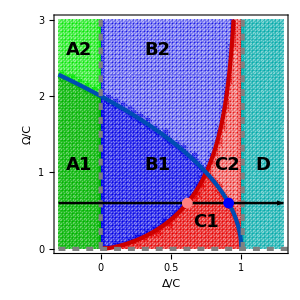

```mathematica
P4=Show[P3,With[{Ω=Ω0},Graphics[{Black,Thickness[0.006],Arrow[{{-0.3,Ω},{1.3,Ω}}]}]],With[{Δ=cs1},Graphics[{Dashed,Blue,PointSize[0.025],Point[{{cs1,Ω0},{cs1,Ω0}}]}]],With[{Δ=cs2},Graphics[{Dashed,Pink,PointSize[0.025],Point[{{cs2,Ω0},{cs2,Ω0}}]}]],
Graphics[{Text[Style["A1",FontFamily->"Arial",Bold,18],{-0.15,1.1}]}],Graphics[{Text[Style["A2",FontFamily->"Arial",Bold,18],{-0.15,2.6}]}],
Graphics[{Text[Style["B1",FontFamily->"Arial",Bold,18],{0.4,1.1}]}],Graphics[{Text[Style["B2",FontFamily->"Arial",Bold,18],{0.4,2.6}]}],Graphics[{Text[Style["C1",FontFamily->"Arial",Bold,18],{0.75,0.35}]}],Graphics[{Text[Style["C2",FontFamily->"Arial",Bold,18],{0.9,1.1}]}],Graphics[{Text[Style["D",FontFamily->"Arial",Bold,18],{1.15,1.1}]}]]
```

```mathematica
PhaseCut=Simplify[Discriminant[Det[ham[Δ,Ω0,γ]-IdentityMatrix[3]e],e]]
```

-4 γ^6+γ^4 (354/25-8 Δ^2)+((91-100 Δ)^2 (43+50 Δ+25 Δ^2))/62500+γ^2 (-10443/625+(162 Δ)/25+(62 Δ^2)/5-4 Δ^4)

```mathematica
Collect[-Det[ham[Δ,Ω,γ]-IdentityMatrix[3]e],e]
a2=-Coefficient[Collect[-Det[ham[Δ,Ω,γ]-IdentityMatrix[3]e],e],e,2];
a1=Coefficient[Collect[-Det[ham[Δ,Ω,γ]-IdentityMatrix[3]e],e],e,1];
a0=-Coefficient[Collect[-Det[ham[Δ,Ω,γ]-IdentityMatrix[3]e],e],e,0];
realcond=(a1-3a0/a2)/2-(a2/3)^2/.{Ω->Ω0}
```

e^3-2 e^2 Δ-Ω^2/2+(Δ Ω^2)/2+e (-1+γ^2+Δ^2-Ω^2/2)

-(4 Δ^2)/9+1/2 (-59/50+γ^2-(3 (9/50-(9 Δ)/50))/(2 Δ)+Δ^2)

```mathematica
gs=γ/.Solve[(realcond/.{Δ->cs2})==0,γ][[2]]
```

1/30 √((243+819 Root0.616Root[-243+243 #1+400 #1^3&,1]0.6157336413227936-100 (Root0.616Root[-243+243 #1+400 #1^3&,1]0.6157336413227936)^3)/(Root0.616Root[-243+243 #1+400 #1^3&,1]0.6157336413227936))

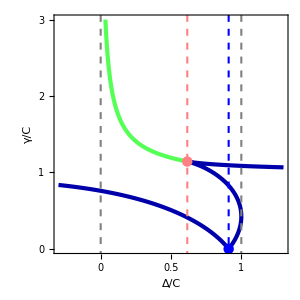

```mathematica
P5=Show[ContourPlot[PhaseCut==0,{Δ,-0.3,1.3},{γ,0,3},PlotPoints->100,ContourStyle->Directive[Darker@Blue,Opacity[1],Thickness[0.01]]],
ContourPlot[realcond==0,{Δ,0,cs2},{γ,0,3},PlotPoints->100,ContourStyle->Directive[Lighter@Green,Opacity[1],Thickness[0.01]]],
Graphics[{Dashed,Thickness[0.005],Gray,Line[{{0,-0.3},{0,3.3}}],Line[{{1,-0.3},{1,3.3}}]}],
With[{Δ=cs1},Graphics[{Dashed,Blue,PointSize[0.025],Point[{{cs1,0}}]}]],
Graphics[{Blue,Dashed,Thickness[0.005],Line[{{cs1,-0.3},{cs1,3.3}}]}],With[{Δ=cs2},Graphics[{Dashed,Pink,PointSize[0.025],Point[{{cs2,N[gs]}}]}]],Graphics[{Pink,Dashed,Thickness[0.005],Line[{{cs2,-0.3},{cs2,3.3}}]}],
Frame->True,PlotTheme->"Scientific",FrameTicks->{{{0,1,2,3},None},{{0,0.5,1},None}},FrameStyle->Directive[Black,18,Thickness[0.0039]],PlotRange->{{-0.3,1.3},{0,3}},ImageSize->300,FrameLabel->{"Δ/C","γ/C"}]
```

```mathematica
P6=Show[RegionPlot[-0.3<Δ<0,{Δ,-0.3,1.2},{Ω,0,3},BoundaryStyle->None,PlotPoints->60,PlotStyle->{RGBColor[0,0.7,0,.6]}],RegionPlot[-0<Δ<cs2,{Δ,-0.3,1.2},{Ω,0,3},BoundaryStyle->None,PlotPoints->60,PlotStyle->{RGBColor[0,0,.9,.5]}],RegionPlot[cs2<Δ<cs1,{Δ,-0.3,1.2},{Ω,0,3},BoundaryStyle->None,PlotPoints->60,PlotStyle->{RGBColor[.9,0,0,.5]}],RegionPlot[cs1<Δ<1,{Δ,-0.3,1.2},{Ω,0,3},BoundaryStyle->None,PlotPoints->60,PlotStyle->{RGBColor[.9,0,0,.3]}],RegionPlot[Δ>1,{Δ,-0.3,1.3},{Ω,0,3},BoundaryStyle->None,PlotPoints->60,PlotStyle->{Darker@Cyan,Opacity[.5]}],P5,Frame->True,PlotTheme->"Scientific",FrameTicks->{{{0,1,2,3},None},{{0,0.5,1},None}},FrameStyle->Directive[Black,18,Thickness[0.0039]],PlotRange->{{-0.3,1.3},{0,3}},ImageSize->300,FrameLabel->{"Δ/C","γ/C"}];
```

## Eigenvalues in different regions

```mathematica
Clear[Δ,Ω,γ]
```

```mathematica
Ω0=0.8;
Δ0=1.15;
ham[Δ_,Ω_,γ_]:=Evaluate[{{Δ-I γ,1,Ω/2},{1,Δ+I γ,Ω/2},{Ω/2,Ω/2,0}}];
ham[Δ,Ω0,γ]//MatrixForm
```

(-ⅈ γ+Δ | 1 | 0.4
1 | ⅈ γ+Δ | 0.4
0.4 | 0.4 | 0)

```mathematica
γlist=Table[i,{i,0,2,0.001}];
γlists=Table[i,{i,1,2,0.001}];
```

```mathematica
eigbr1={#,SortBy[Eigenvalues[ham[Δ0,Ω0,#]],Re][[1]]}&/@γlist;
eigbr2={#,SortBy[Eigenvalues[ham[Δ0,Ω0,#]],Re][[2]]}&/@γlist;
eigbr3={#,SortBy[Eigenvalues[ham[Δ0,Ω0,#]],Re][[3]]}&/@γlist;
eigbrs1={#,SortBy[Eigenvalues[ham[Δ0,Ω0,#]],Re][[1]]}&/@γlists;
eigbrs2={#,SortBy[Eigenvalues[ham[Δ0,Ω0,#]],Re][[2]]}&/@γlists;
eigbrs3={#,SortBy[Eigenvalues[ham[Δ0,Ω0,#]],Re][[3]]}&/@γlists;
eigbi1={#,SortBy[Eigenvalues[ham[Δ0,Ω0,#]],Im][[1]]}&/@γlist;
eigbi2={#,SortBy[Eigenvalues[ham[Δ0,Ω0,#]],Im][[2]]}&/@γlist;
eigbi3={#,SortBy[Eigenvalues[ham[Δ0,Ω0,#]],Im][[3]]}&/@γlist;
eigbis1={#,SortBy[Eigenvalues[ham[Δ0,Ω0,#]],Im][[1]]}&/@γlists;
eigbis2={#,SortBy[Eigenvalues[ham[Δ0,Ω0,#]],Im][[2]]}&/@γlists;
eigbis3={#,SortBy[Eigenvalues[ham[Δ0,Ω0,#]],Im][[3]]}&/@γlists;

γlist=Table[i,{i,0.001,2,0.0003}];
γlists=Table[i,{i,1,2,0.0003}];
eigver1 ={#^(1/2),Eigenvectors[ham[Δ0,Ω0,#]][[1]]}&/@γlist;
hop1 = Re[eigver1 *Conjugate[eigver1]];
eigver2 ={#^(1/2),Eigenvectors[ham[Δ0,Ω0,#]][[2]]}&/@γlist;
hop2 = Re[eigver2 *Conjugate[eigver2]];
eigver3 ={#^(1/2),Eigenvectors[ham[Δ0,Ω0,#]][[3]]}&/@γlist;
hop3 = Re[eigver3 *Conjugate[eigver3]];


(*Show[Graphics[{Red,Thickness[0.001],Point[{#[[1]],#[[2]][[1]]}&/@hop1]}],(*Graphics[{Green,Thickness[0.001],Point[{#[[1]],#[[2]][[2]]}&/@hop1]}],*)
Graphics[{Blue,Thickness[0.001],Point[{#[[1]],#[[2]][[3]]}&/@hop1]}],
Graphics[{PointSize[Large],Point[{3(3)^(1/2)/4,0.33}]}],
Graphics[{Text[Style["3",FontFamily->"Arial",(*Bold,*)18],{0.15,0.15}]}],Graphics[{Text[Style["2",FontFamily->"Arial",(*Bold,*)18],{0.15,0.4}]}],Graphics[{Text[Style["1",FontFamily->"Arial",(*Bold,*)18],{0.15,0.49}]}],
Graphics[{Text[Style["2",FontFamily->"Arial",(*Bold,*)18],{1.42,0.1}]}],Graphics[{Text[Style["3",FontFamily->"Arial",(*Bold,*)18],{1.59,0.2}]}],Graphics[{Text[Style["1",FontFamily->"Arial",(*Bold,*)18],{1.4,0.75}]}],
PlotRange->All,Frame->True,FrameStyle->Directive[Black,16,Thickness[0.003]],FrameTicks->{{{0,0.2,0.4,0.6,0.8},None},{{0,1,2},None}},FrameLabel->{{"Hopfield Coefficient",None},{"γ/C","eigen-state A"}},AspectRatio->2/1,ImageSize->{Automatic,350}]

Show[Graphics[{Red,Thickness[0.001],Point[{#[[1]],#[[2]][[1]]}&/@hop2]}],
Graphics[{Green,Thickness[0.001],Point[{#[[1]],#[[2]][[2]]}&/@hop2]}],
Graphics[{Blue,Thickness[0.001],Point[{#[[1]],#[[2]][[3]]}&/@hop2]}],
Graphics[{PointSize[Large],Point[{3(3)^(1/2)/4,0.33}]}],
Graphics[{Text[Style["2",FontFamily->"Arial",(*Bold,*)18],{0.15,0.15}]}],Graphics[{Text[Style["3",FontFamily->"Arial",(*Bold,*)18],{0.15,0.4}]}],Graphics[{Text[Style["1",FontFamily->"Arial",(*Bold,*)18],{0.15,0.49}]}],
Graphics[{Text[Style["1",FontFamily->"Arial",(*Bold,*)18],{1.42,0.1}]}],Graphics[{Text[Style["3",FontFamily->"Arial",(*Bold,*)18],{1.59,0.2}]}],Graphics[{Text[Style["2",FontFamily->"Arial",(*Bold,*)18],{1.4,0.75}]}],
PlotRange->All,Frame->True,FrameStyle->Directive[Black,16,Thickness[0.003]],FrameTicks->{{None,None},{{0,1,2},None}},FrameLabel->{{None,None},{"γ/C","eigen-state B"}},AspectRatio->2/1,ImageSize->{Automatic,350}]

Show[Graphics[{Red,Thickness[0.001],Point[{#[[1]],#[[2]][[1]]}&/@hop3]}],
(*Graphics[{Green,Thickness[0.001],Point[{#[[1]],#[[2]][[2]]}&/@hop3]}],*)
Graphics[{Blue,Thickness[0.001],Point[{#[[1]],#[[2]][[3]]}&/@hop3]}],
Graphics[{PointSize[Large],Point[{3(3)^(1/2)/4,0.33}]}],
Graphics[{Text[Style["1",FontFamily->"Arial",(*Bold,*)18],{0.15,0.15}]}],Graphics[{Text[Style["3",FontFamily->"Arial",(*Bold,*)18],{0.15,0.4}]}],Graphics[{Text[Style["2",FontFamily->"Arial",(*Bold,*)18],{0.15,0.49}]}],
Graphics[{Text[Style["2",FontFamily->"Arial",(*Bold,*)18],{1.42,0.1}]}],Graphics[{Text[Style["1",FontFamily->"Arial",(*Bold,*)18],{1.59,0.2}]}],Graphics[{Text[Style["3",FontFamily->"Arial",(*Bold,*)18],{1.4,0.75}]}],
PlotRange->All,Frame->True,FrameStyle->Directive[Black,16,Thickness[0.003]],FrameTicks->{{None,None},{{0,1,2},None}},FrameLabel->{{None,None},{"γ/C","eigen-state C"}},
AspectRatio->2/1,ImageSize->{Automatic,350}]*)
```

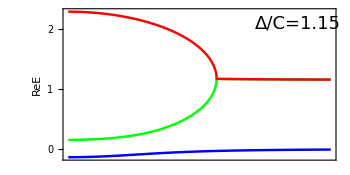

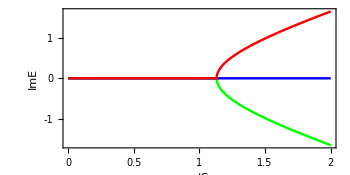

```mathematica
Show[Graphics[{Blue,Thickness[0.005],Line[{#[[1]],Re[#[[2]]]}&/@eigbr1]}],
Graphics[{Green,Thickness[0.005],Line[{#[[1]],Re[#[[2]]]}&/@eigbr2]}],
Graphics[{Red,Thickness[0.005],Line[{#[[1]],Re[#[[2]]]}&/@eigbr3]}],
(*Graphics[{Blue,Thickness[0.005],Line[{#[[1]],Re[#[[2]]]}&/@eigbrs1]}],
Graphics[{Green,Thickness[0.005],Line[{#[[1]],Re[#[[2]]]}&/@eigbrs2]}],
Graphics[{Red,Thickness[0.005],Line[{#[[1]],Re[#[[2]]]}&/@eigbrs3]}],
Graphics[{Text[Style["+",FontFamily->"Arial",(*Bold,*)18],{0.1,1.75}]}],Graphics[{Text[Style["-",FontFamily->"Arial",(*Bold,*)18],{0.1,0}]}],Graphics[{Text[Style["+",FontFamily->"Arial",(*Bold,*)18],{0.1,-.5}]}],
Graphics[{Text[Style["EP3",FontFamily->"Arial",(*Bold,*)18],{3(3)^(1/2)/4-0.2,1/2}]}],
Graphics[{PointSize[Large],Point[{3(3)^(1/2)/4+0.005,1/2}]}],*)
Graphics[{Text[Style["Δ/C=1.15",FontFamily->"Arial",(*Bold,*)18],{1.75,2.1}]}],
Graphics[{Text[Style["",FontFamily->"Arial",(*Bold,*)18],{0.1,-1}]}],
PlotRange->All,Frame->True,FrameStyle->Directive[Black,16,Thickness[0.003]],FrameTicks->{{{2,0,1,-1},None},{None,None}},FrameLabel->{None,"ReE"},AspectRatio->1/2,ImageSize->{350,Automatic}]
Show[Graphics[{Green,Thickness[0.005],Line[{#[[1]],Im[#[[2]]]}&/@eigbi1]}],
Graphics[{Blue,Thickness[0.005],Line[{#[[1]],Im[#[[2]]]}&/@eigbi2]}],
Graphics[{Red,Thickness[0.005],Line[{#[[1]],Im[#[[2]]]}&/@eigbi3]}],
(*Graphics[{Red,Thickness[0.005],Line[{#[[1]],Im[#[[2]]]}&/@eigbis1]}],
Graphics[{Blue,Thickness[0.005],Line[{#[[1]],Im[#[[2]]]}&/@eigbis2]}],
Graphics[{Green,Thickness[0.005],Line[{#[[1]],Im[#[[2]]]}&/@eigbis3]}],
Graphics[{PointSize[Large],Point[{3(3)^(1/2)/4+0.005,0}]}],*)
PlotRange->All,Frame->True,FrameStyle->Directive[Black,16,Thickness[0.003]],FrameTicks->{{{-1,0,1},None},{{0,0.5,1,1.5,2},None}},FrameLabel->{"γ/C","ImE"},AspectRatio->1/2,ImageSize->{350,Automatic}]
```

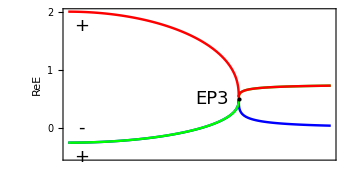
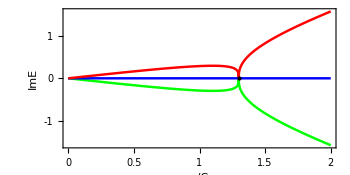

```mathematica
Plot[Evaluate[Re[Eigenvalues[ham[Δ0,Ω0,γ]]]],{γ,0,3},PlotStyle->{{Thickness[0.008]}},PlotRange->All,Frame->True,FrameStyle->Directive[Black,16],FrameLabel->{"G","ReE"}]*)
```

```mathematica
With[{Δ=Δ0},Plot[Evaluate[ComplexExpand@Re[Eigenvalues[ham[Δ,Ω0,γ]]]],{γ,0,3},PlotStyle->{{Thickness[0.008]}},PlotRange->All,Frame->True,FrameStyle->Directive[Black,16],FrameLabel->{"γ/C","ReE"}]]
With[{Δ=Δ0},Plot[Evaluate[ComplexExpand[Im[Eigenvalues[ham[Δ,Ω0,γ]]]]],{γ,0,3},PlotStyle->{{Thickness[0.008]}},PlotRange->All,Frame->True,FrameStyle->Directive[Black,16],FrameLabel->{"G","ReE"}]]*)
```

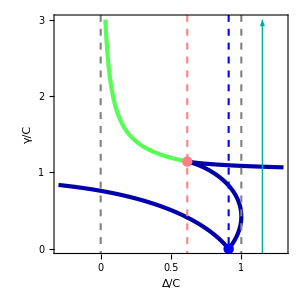

```mathematica
Show[P5,Graphics[{Darker@Cyan,Arrow[{{Δ0,-0.3},{Δ0,3}}]}]]
```

Parameters: 
Ω0/C=3/5;
Δ/C={-0.15,0.3,N@cs2,0.8,0.98,1.15}

## Exciton-Polariton Parity Analysis

```mathematica
(*Plot[Evaluate[Re@Eigenvalues[ham[Δ,Ω0,0]]],{Δ,0,1}]*)
```

```mathematica
(*P={{0,1,0},{1,0,0},{0,0,1}};
b=Eigensystem[ham[0.8,Ω0,0]];
b//MatrixForm
Chop[P.b[[2,1]]-b[[2,1]]]
Chop[P.b[[2,2]]-b[[2,2]]]
Chop[P.b[[2,3]]+b[[2,3]]]*)
```

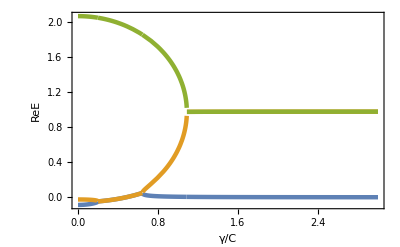
```mathematica
(*-Graphics-*)
```

```mathematica
(*-Graphics-*)
```

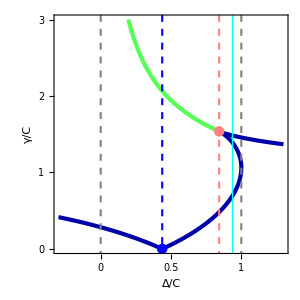
```mathematica
(*-Graphics-*)
```

```mathematica
(*({{Δ, 1, 3/4}, {1, Δ, 3/4}, {3/4, 3/4, 0}})*)
```

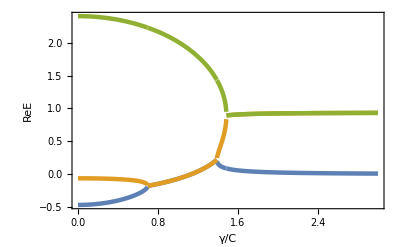
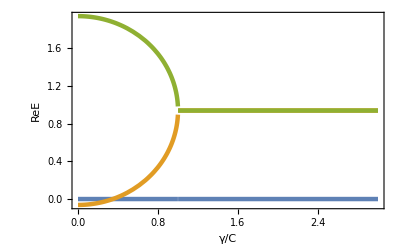

```mathematica
(*a=Eigensystem[({{1.2-0.4, 1, Ω0/2}, {1, 1.2-.4, Ω0/2}, {Ω0/2, Ω0/2, 0}})];
N[a]//MatrixForm*)
```

```mathematica
(*P={{0,1,0},{1,0,0},{0,0,1}}
P.P//MatrixForm*)
```

```mathematica
(*Chop[P.a[[2,1]]-a[[2,1]]]
Chop[P.a[[2,2]]+a[[2,2]]]
Chop[P.a[[2,3]]-a[[2,3]]]*)
```